# k effecton on τα

## 3D Voronoi

### load data

```mathematica
s0s3D={5.45};
```

```mathematica
temperatures3D={{0.075,0.035,0.0162,0.0073,0.0032,0.0014,0.000565,0.000255,0.00011,0.0000525,0.0000182,0.00000813,0.0000034}};records=Table[i,{i,0,9}];
```

```mathematica
tauList=Table[Round[10^(i/3)],{i,0,12}]
```

{1,2,5,10,22,46,100,215,464,1000,2154,4642,10000}

```mathematica
tauEstimate[t_]:=If[t<=1000,Table[i*1000,{i,0,9}],Table[If[t*i<10000,1000*i,t*i],{i,0,9}]]
```

```mathematica
tauEstimate[10000]
```

{0,1000,20000,30000,40000,50000,60000,70000,80000,90000}

```mathematica
test=Import["/home/chengling/Research/Project/Cell/3dVoronoi/data/productionRuns/N512/s5.450/fs/Fs_N512_s5.4500_T0.01620000_k11.000000_waitingTime2000_idx6.nc"]
```

```mathematica
fs3Ddata=Table[Table[Table[DeleteCases[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/3dVoronoi/data/productionRuns/N512/s","/fs/Fs_N512_s","_T","_k","_waitingTime","_idx",".nc"},{s0s[[s]],s0s[[s]],temperatures[[s,T]],k,tauEstimate[tauList[[T]]][[wt]],i},{3,4,8,6,0,0}],"Data"],{wt,10}],$Failed],{i,0,9}],{}],{T,Length[temperatures3D[[s]]]}],{s,Length[s0s]}],{k,2.0,26.0,2}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/3dVoronoi/data/productionRuns/N512/s5.450/fs/Fs_N512_s5.4500_T0.07500000_k2.000000_waitingTime0_idx5.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/3dVoronoi/data/productionRuns/N512/s5.450/fs/Fs_N512_s5.4500_T0.07500000_k2.000000_waitingTime1000_idx5.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/3dVoronoi/data/productionRuns/N512/s5.450/fs/Fs_N512_s5.4500_T0.07500000_k2.000000_waitingTime2000_idx5.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
fs3DMean=Table[Table[Table[Table[Mean[Flatten[Table[Table[Normal[If[Length[fs3Ddata[[k,s,T,i,wt,2]]]<t,Nothing,fs3Ddata[[k,s,T,i,wt,2,t]]]],{wt,Length[fs3Ddata[[k,s,T,i]]]}],{i,Length[fs3Ddata[[k,s,T]]]}]]],{t,Max[Length/@Flatten[fs3Ddata[[k,s,T,;;,;;,2]]]]}],{T,Length[fs3Ddata[[k,s]]]}],{s,Length[s0s]}],{k,Length[fs3Ddata]}];
```

```mathematica
timelist3D=Normal[fs3Ddata[[1,1,13,1,1,1]]]-fs3Ddata[[1,1,13,1,1,1,1]];
```

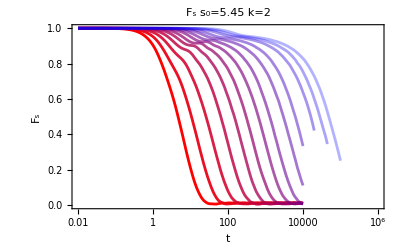
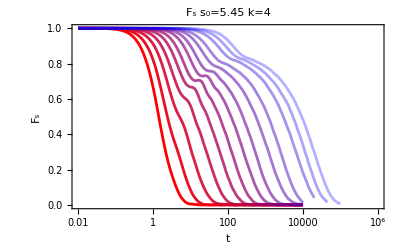
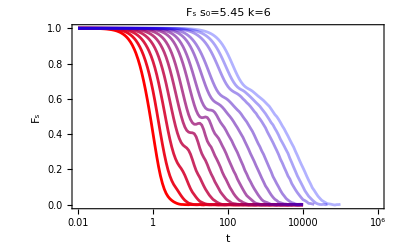
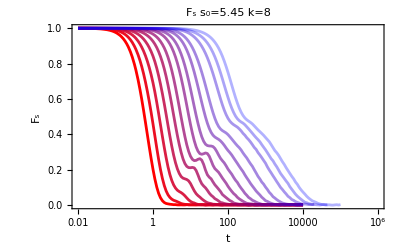
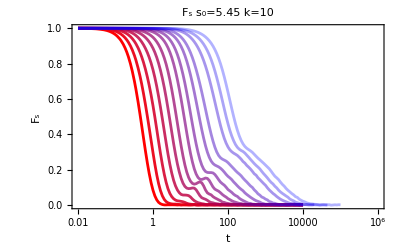
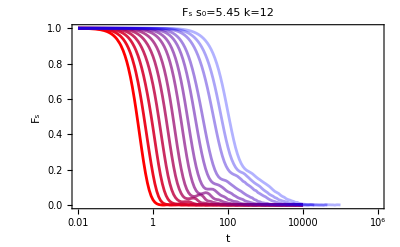
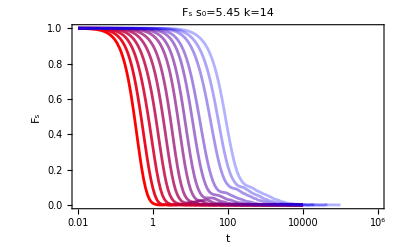
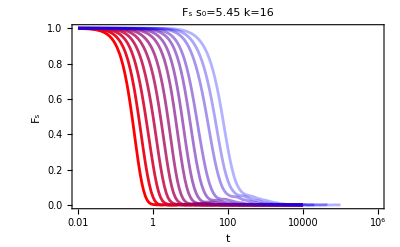

```mathematica
fs3DMeanPlot=Table[Table[ListLogLinearPlot[Table[Table[{timelist3D[[t]],fs3DMean[[k,s,T,t]]},{t,Length[fs3DMean[[k,s,T]]]}],{T,Length[temperatures3D[[s]]]}],PlotStyle->redBluePlotConfig[Length[temperatures3D[[s]]]],Joined->True,FrameLabel->{"t","F_s"},PlotLabel->"F_s s_0="<>ToString[s0s[[s]]]<>" k="<>ToString[(k)*2],ImageSize->400,PlotRange->{{0.01,10^6},All}],{s,Length[s0s]}],{k,Length[fs3Ddata]}]
```

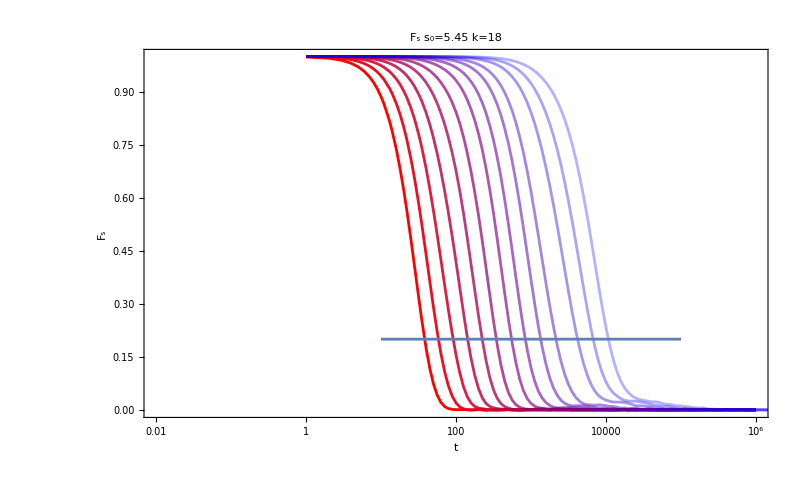

```mathematica
Table[Table[Show[ListLogLinearPlot[Table[Table[{timelist3D[[t]]*100,fs3DMean[[k,s,T,t]]},{t,Length[fs3DMean[[k,s,T]]]}],{T,Length[temperatures3D[[s]]]}],PlotStyle->redBluePlotConfig[Length[temperatures3D[[s]]]],Joined->True,FrameLabel->{"t","F_s"},PlotLabel->"F_s s_0="<>ToString[s0s[[s]]]<>" k="<>ToString[(k)*2],ImageSize->800,PlotRange->{{0.01,10^6},All}],LogLinearPlot[0.2,{x,10,100000}]],{s,Length[s0s]}],{k,{Length[fs3Ddata]-4}}]
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_18/fs_3D_k.jpeg",Grid[Partition[fs3DMeanPlot[[;;9,1]],3]],ImageResolution->300];
```

```mathematica
tauAlpha3D={38,60,94,140,230,350,550,830,1300,2200,4000,7000,11000}/100;
```

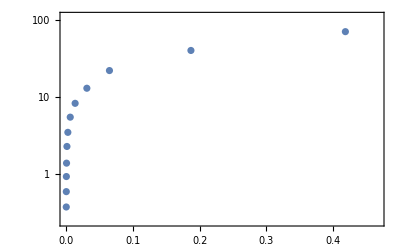

```mathematica
ListLogPlot[Table[{temperatures3D[[1,-1]]/temperatures3D[[1,T]],tauAlpha3D[[T]]},{T,Length[tauAlpha3D]}]]
```

## 2D Voronoi

### data loading

```mathematica
p0s={3.825};
```

```mathematica
temperatures2D={{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005}};
 records2D={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate2D={{ 1, 1, 1,1, 1,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500,5000,10000}};
```

```mathematica
test=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.825/timeCRSISF_N4096_p3.8250_T0.00100000_k11.000_waitingTime15000_idx18.nc","D"]
```

```mathematica
crFs2Ddata=Table[Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeCRSISF_N4096_p","_T","_k","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures2D[[p,T]],k,Floor[If[tauEstimate2D[[p,T]]==999999,tauEstimate2D[[p,T]],If[tauEstimate2D[[p,T]]<1000,10000,tauEstimate2D[[p,T]]*10]]
],records2D[[p,i]]},{3,4,8,3,0,0}],"Data"],{i,Length[records2D[[p]]]}],$Failed],{T,Length[temperatures2D[[p]]]}],{p,Length[p0s]}],{k,2.0,26.0,2}];
```

```mathematica
fs2DMean=Table[Table[Table[Table[Mean[Table[If[Length[crFs2Ddata[[k,p,T,i,2]]]>=rec,crFs2Ddata[[k,p,T,i,2,rec]],Nothing],{i,Length[crFs2Ddata[[k,p,T]]]}]],{rec,Max[Table[Length[crFs2Ddata[[k,p,T,i,1]]],{i,Length[crFs2Ddata[[k,p,T]]]}]]}],{T,Length[temperatures2D[[p]]]}],{p,Length[p0s]}],{k,Length[crFs2Ddata]}];
```

```mathematica
fs2DMean[[1,1,1]]
```

{{0.,1.},{0.01,0.999985},{0.02,0.99994},{0.03,0.999866},{0.04,0.999761},{0.05,0.999627},{0.06,0.999462},{0.07,0.999269},{0.08,0.999045},{0.09,0.998793},{0.1,0.99851},{0.11,0.998199},{0.13,0.997489},{0.14,0.997091},{0.16,0.996209},{0.18,0.995215},{0.2,0.99411},{0.22,0.992896},{0.25,0.990877},{0.28,0.988626},{0.32,0.985281},{0.35,0.982526},{0.4,0.977496},{0.45,0.97196},{0.5,0.965968},{0.56,0.958248},{0.63,0.948623},{0.71,0.93698},{0.79,0.924839},{0.89,0.909235},{1.,0.891862},{1.12,0.873031},{1.26,0.851595},{1.41,0.829578},{1.58,0.806007},{1.78,0.780193},{2.,0.754055},{2.24,0.728078},{2.51,0.702078},{2.82,0.676521},{3.16,0.652963},{3.55,0.629897},{3.98,0.606831},{4.47,0.580706},{5.01,0.550661},{5.62,0.515852},{6.31,0.476382},{7.08,0.43454},{7.94,0.393066},{8.91,0.354},{10.,0.314136},{11.22,0.272521},{12.59,0.231997},{14.13,0.193908},{15.85,0.157106},{17.78,0.122397},{19.95,0.0934787},{22.39,0.071037},{25.12,0.0495412},{28.18,0.035426},{31.62,0.0229573},{35.48,0.0100029},{39.81,0.00575161},{44.67,0.003188},{50.12,0.0014454},{56.23,-0.00184026},{63.1,-0.00126478},{70.79,-0.00101068},{79.43,-0.00135979},{89.13,0.00185882},{100.,0.00100015},{112.2,-0.000388677},{125.89,-0.000160508},{141.25,0.00165073},{158.49,-0.00117087},{177.83,-0.00108839},{199.53,-0.0014158},{223.87,-0.000509038},{251.19,0.000993554},{281.84,-0.00117442},{316.23,-0.00024292},{354.81,0.000144015},{398.11,0.000944354},{446.68,0.000275101},{501.19,0.00125533},{562.34,-0.00171881},{630.96,0.0003831},{707.95,-0.000224303},{794.33,0.000796555},{891.25,-0.0000452983},{1000.,-0.000498997},{1122.02,0.00101297},{1258.93,-0.000556225},{1412.54,-0.0000363389},{1584.89,-0.00109079},{1778.28,0.000460034},{1995.26,-0.000686694},{2238.72,0.0000431968},{2511.89,-0.000489873},{2818.38,-0.000366106},{3162.28,-0.000134558},{3548.13,-0.000521423},{3981.07,-0.000310859},{4466.84,0.000392597},{5011.87,-0.000410158},{5623.41,0.00141762},{6309.57,-0.000533234},{7079.46,0.000621484},{7943.28,-0.0000510355},{8912.51,0.00030169},{10000.,-0.0000741959}}

```mathematica
timelist2D=Normal[crFs2Ddata[[1,1,-1,3,1]]]-crFs2Ddata[[1,1,-1,3,1,1]]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2}

```mathematica
tauAlpha2D={14,28,46,89,180,250,350,500,750,1100,1600,2300,4000,10000,28000};
```

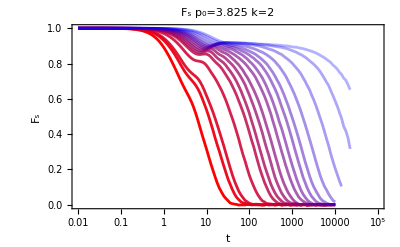
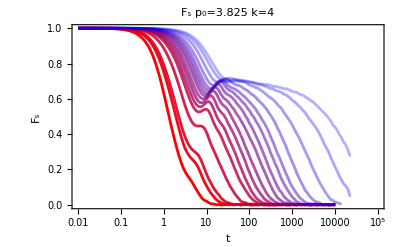
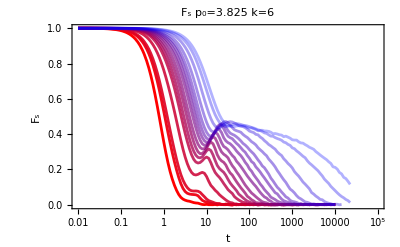
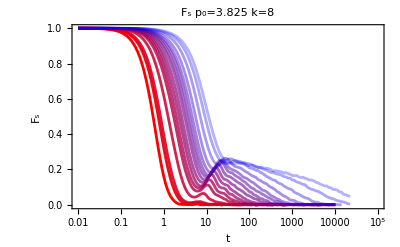
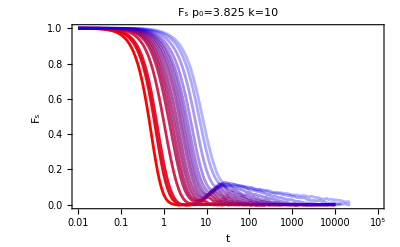
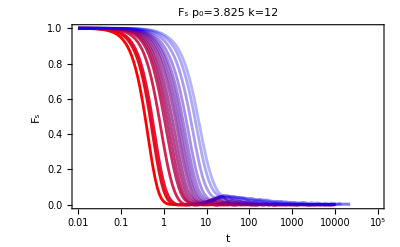
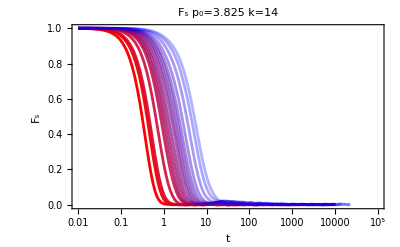
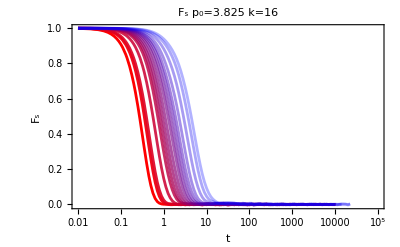

```mathematica
fs2DMeanPlot=Table[Table[Show[ListLogLinearPlot[Table[Table[{timelist2D[[t]],fs2DMean[[k,s,T,t]]},{t,Length[fs2DMean[[k,s,T]]]}],{T,Length[temperatures2D[[s]]]}],PlotStyle->redBluePlotConfig[Length[temperatures2D[[s]]]],Joined->True,FrameLabel->{"t","F_s"},PlotLabel->"F_s p_0="<>ToString[p0s[[s]]]<>" k="<>ToString[(k)*2],ImageSize->400,PlotRange->{{0.01,10^5},All}]],{s,Length[p0s]}],{k,Length[crFs2Ddata]}]
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_18/fs_2D_k.jpeg",Grid[Partition[fs2DMeanPlot[[;;9,1]],3]],ImageResolution->300];
```

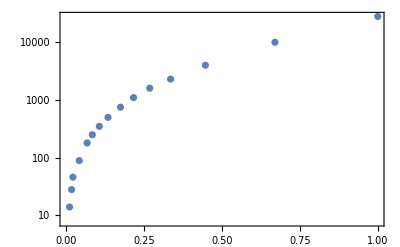

```mathematica
ListLogPlot[Table[{temperatures2D[[1,-2]]/temperatures2D[[1,T]],tauAlpha2D[[T]]},{T,Length[tauAlpha2D]}]]
```

## Vitrimer

```mathematica
rhos={0.92333,2.42954};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0695_rho2.42954_k2.dat","Data"]
```

{}

```mathematica
files=Table[Table[FileNames["Fs_T*_rho"<>ToString[rhos[[rho]]]<>"_k"<>ToString[k]<>".dat","/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/"],{k,2,20,2}],{rho,Length[rhos]}];
```

```mathematica
Length[fsMCThighnames]
```

51

```mathematica
names =Table[Table[FileNameTake/@files[[rho,k]],{k,Length[files[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
StringReplace[#,StartOfString~~"Fs_T"~~t__~~"_rho2.42954_k2.dat":>t]&/@names[[2,1]]
```

{0.001,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.04,0.05,0.061,0.062,0.063,0.064,0.065,0.0685,0.068,0.0695,0.069,0.06,0.07,0.08,0.09,0.15,0.1,0.3}

```mathematica
temperaturesVtrimer=Table[StringReplace[#,StartOfString~~"Fs_T"~~t__~~"_rho"<>ToString[rhos[[rho]]]<>"_k"<>ToString[2]<>".dat":>t]&/@names[[rho,1]],{rho,Length[rhos]}]
```

{{0.000175,0.0001,0.00025,0.00035,0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.007,0.008,0.009,0.015,0.01,0.03,0.05,0.06,0.07,0.08,0.09,0.15,0.1,0.5,0.65,1.5e-06,1e-05,1e-06,1e-07,1e-08,1e-09,2.5e-07,2.5e-08,2.5e-09,2e-05,2e-06,3.5e-06,4e-05,5e-05,5e-06,5e-07,5e-08,5e-09,6.5e-06,6e-07,7.5e-08,7.5e-09,7e-07,8e-06,8e-07},{0.001,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.04,0.05,0.061,0.062,0.063,0.064,0.065,0.0685,0.068,0.0695,0.069,0.06,0.07,0.08,0.09,0.15,0.1,0.3}}

```mathematica
temperaturesVtrimer=Table[ToExpression@StringReplace[temperaturesVtrimer[[rho]],("e")->"*^"],{rho,Length[rhos]}]
```

{{0.000175,0.0001,0.00025,0.00035,0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.007,0.008,0.009,0.015,0.01,0.03,0.05,0.06,0.07,0.08,0.09,0.15,0.1,0.5,0.65,1.5×10^-6,1/100000,1/1000000,1/10000000,1/100000000,1/1000000000,2.5×10^-7,2.5×10^-8,2.5×10^-9,1/50000,1/500000,3.5×10^-6,1/25000,1/20000,1/200000,1/2000000,1/20000000,1/200000000,6.5×10^-6,3/5000000,7.5×10^-8,7.5×10^-9,7/10000000,1/125000,1/1250000},{0.001,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.04,0.05,0.061,0.062,0.063,0.064,0.065,0.0685,0.068,0.0695,0.069,0.06,0.07,0.08,0.09,0.15,0.1,0.3}}

```mathematica
Length[fileshigh]
```

51

```mathematica
idx=Table[Reverse[Ordering[temperaturesVtrimer[[rho]]]],{rho,Length[rhos]}]
```

{{26,25,23,24,22,21,20,19,18,17,15,16,14,13,12,11,9,10,7,6,8,5,4,3,1,2,40,39,36,28,50,45,41,38,37,27,29,51,49,46,42,33,30,47,43,34,31,48,44,35,32},{26,24,25,23,22,21,18,19,16,17,15,14,13,12,11,20,10,9,8,6,7,5,4,3,2,1}}

```mathematica
sortedFilenamesVitrimer=Table[Table[fileslow[[rho,k]][[idx[[rho]]]],{k,Length[files[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
sortedTemperaturesVitrimer=Table[temperaturesVtrimer[[rho,idx[[rho]]]],{rho,Length[rhos]}]
```

{{0.65,0.5,0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,1/50000,1/100000,1/125000,6.5×10^-6,1/200000,3.5×10^-6,1/500000,1.5×10^-6,1/1000000,1/1250000,7/10000000,3/5000000,1/2000000,2.5×10^-7,1/10000000,7.5×10^-8,1/20000000,2.5×10^-8,1/100000000,7.5×10^-9,1/200000000,2.5×10^-9,1/1000000000},{0.3,0.15,0.1,0.09,0.08,0.07,0.0695,0.069,0.0685,0.068,0.065,0.064,0.063,0.062,0.061,0.06,0.05,0.04,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.001}}

```mathematica
fsVitrimer=Table[Table[Import[#,"Data"]&/@sortedFilenamesLow[[rho,k]],{k,Length[files[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
temperatures
```

{{0.01,0.05,0.0025,0.0022,0.001,0.0005,0.0001,0.00005},{0.008,0.007,0.0065,0.0058,0.054}}

```mathematica
tauAlpha*0.06
```

{{0.54,0.12,1.62,1.74,3.36,9.6}}

```mathematica
Position[N[sortedTemperaturesLow],0.01]
```

{{12}}

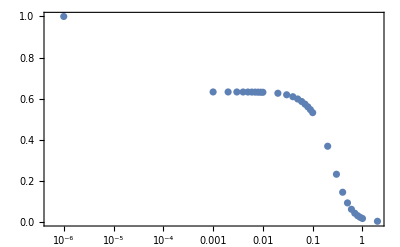

```mathematica
ListLogLinearPlot[fslow[[12,;;,1;;2]]]
```

```mathematica
fsVitrimer[[2,1,7]]
```

{}

```mathematica
sortedFilenamesVitrimer[[2,1,7]]
```

/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0695_rho2.42954_k2.dat

```mathematica
Table[Dimensions[fsVitrimer[[2,1,i]]],{i,Length[fsVitrimer[[2,1]]]}]
```

{{43,3},{48,3},{55,3},{62,3},{49,3},{142,3},{0},{69,3},{51,3},{142,3},{142,3},{57,3},{128,3},{102,3},{143,3},{142,3},{142,3},{142,3},{126,3},{142,3},{142,3},{142,3},{142,3},{122,3},{74,3},{73,3}}

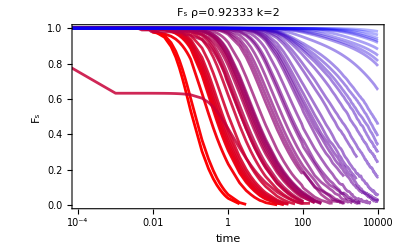
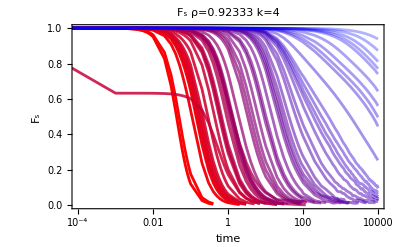
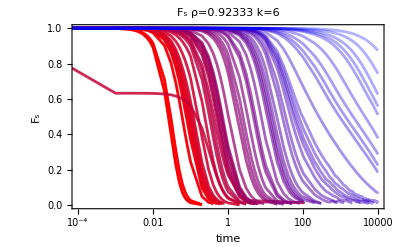
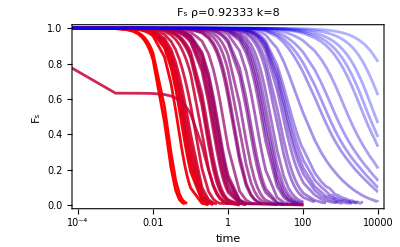
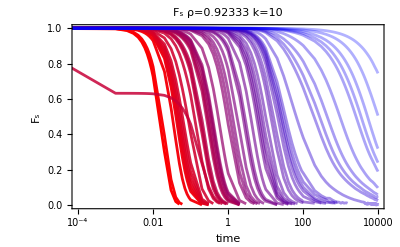
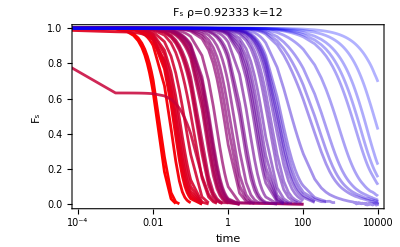
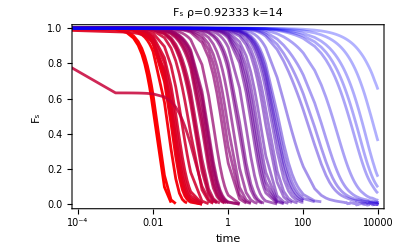
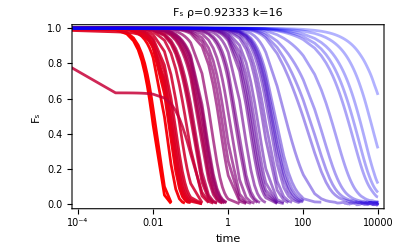

```mathematica
fsVitrimerPLot=Table[Table[Show[ListLogLinearPlot[Table[If[Length[fsVitrimer[[rho,k,T]]]>0,fsVitrimer[[rho,k,T,;;,1;;2]],Nothing],{T,Length[fsVitrimer[[rho,k]]]}],ImageSize->400,PlotRange->{{0.0001,All},All},PlotStyle->redBluePlotConfig[Length[fsVitrimer[[rho,k]]]],Joined->True,PlotLabel->"F_s ρ="<>ToString[rhos[[rho]]]<>" k="<>ToString[(k)*2],FrameLabel->{"time","F_s"}]],{k,Length[files[[rho]]]}],{rho,Length[rhos]}]
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_18/fs_vtrimer_low_k.jpeg",Grid[Partition[fsVitrimerPLot[[1,;;9]],3]],ImageResolution->300];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_18/fs_vtrimer_high_k.jpeg",Grid[Partition[fsVitrimerPLot[[2,;;9]],3]],ImageResolution->300];
```